```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/PV/larin/gamma+Z/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
norm=Expand[Normal[Series[FullSimplify[1/factor invff],{eps,0,2}]]/(I/(16 Pi^2))]
```

1-(π^2 eps^2)/12

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
DEN[p1+p2,mZ,1]=1/(s-mZ^2);
```

```mathematica
(* DEN[___]:=0 *)
```

```mathematica
<<cross-sectionNLOLarin.res
```

```mathematica
(* X[a_]:=norm *)
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=(15)^2;mt=173;fBc=1;R1=R2=√((Pi m)/3) fBc;AL=1/137;mZ=91.2;mW=80.4;cw=mW/mZ;sw=Sqrt[1-cw^2]; nf=6;
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=15^2;mt=175;R1=R2=1;nf=6;AL=1/137;mZ=91.2;mW=80.4;cw=mW/mZ;sw=Sqrt[1-cw^2];
```

```mathematica
Sqrt[4 m^2]
```

12.8

```mathematica
(2mc+2 mc)^2
```

36.

```mathematica
pow[a_,b_]:=a^b
```

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}]
```

-4.85981×10^-12 eps Aconj(1.5) AS^3-(1.81801×10^-13 Aconj(1.5) AS^3)/eps+6.15743×10^-12 Aconj(1.5) AS^3-5.10861×10^-13 eps Aconj(4.9) AS^3+(5.56534×10^-14 Aconj(4.9) AS^3)/eps+3.70878×10^-12 Aconj(4.9) AS^3-7.91976×10^-14 eps Aconj(175.) AS^3+2.36294×10^-13 Aconj(175.) AS^3-6.72951×10^-11 eps Bconj(12.3596,0.,0.) AS^3+6.57848×10^-11 Bconj(12.3596,0.,0.) AS^3+1.70484×10^-13 eps Bconj(12.3596,1.5,1.5) AS^3+(1.61916×10^-12 Bconj(12.3596,1.5,1.5) AS^3)/eps-4.70063×10^-12 Bconj(12.3596,1.5,1.5) AS^3-3.42996×10^-12 eps Bconj(12.3596,4.9,4.9) AS^3-9.14231×10^-12 Bconj(12.3596,4.9,4.9) AS^3-4.83447×10^-9 eps Bconj(12.3596,175.,175.) AS^3-7.27779×10^-9 Bconj(12.3596,175.,175.) AS^3-4.88489×10^-13 eps Bconj(51.9348,1.5,4.9) AS^3-(2.08275×10^-12 Bconj(51.9348,1.5,4.9) AS^3)/eps+5.43293×10^-12 Bconj(51.9348,1.5,4.9) AS^3-5.24611×10^-12 eps Bconj(51.9348,4.9,1.5) AS^3-(2.08275×10^-12 Bconj(51.9348,4.9,1.5) AS^3)/eps+3.11049×10^-12 Bconj(51.9348,4.9,1.5) AS^3+3.74723×10^-11 eps Bconj(76.7444,0.,4.9) AS^3+3.09542×10^-11 Bconj(76.7444,0.,4.9) AS^3+7.86915×10^-11 eps Bconj(76.7444,4.9,0.) AS^3-1.28451×10^-10 Bconj(76.7444,4.9,0.) AS^3-6.17397×10^-11 eps Bconj(131.891,0.,0.) AS^3+6.8825×10^-12 Bconj(131.891,0.,0.) AS^3-1.35447×10^-12 eps Bconj(131.891,1.5,1.5) AS^3+2.56704×10^-12 Bconj(131.891,1.5,1.5) AS^3+1.20899×10^-13 eps Bconj(131.891,4.9,4.9) AS^3+(1.61916×10^-12 Bconj(131.891,4.9,4.9) AS^3)/eps+7.29593×10^-13 Bconj(131.891,4.9,4.9) AS^3+3.32525×10^-11 eps Bconj(131.891,175.,175.) AS^3+3.62573×10^-11 Bconj(131.891,175.,175.) AS^3+1.19802×10^-10 eps Bconj(174.516,0.,1.5) AS^3-3.51735×10^-11 Bconj(174.516,0.,1.5) AS^3+1.8796×10^-11 eps Bconj(174.516,1.5,0.) AS^3-2.10036×10^-12 Bconj(174.516,1.5,0.) AS^3-1.73056×10^-14 eps Bconj(225.,0.,0.) AS^3+6.69633×10^-15 Bconj(225.,0.,0.) AS^3-7.52123×10^-11 eps Bconj(225.,1.5,1.5) AS^3+2.82747×10^-11 Bconj(225.,1.5,1.5) AS^3+1.80636×10^-11 eps Bconj(225.,4.9,4.9) AS^3-2.89394×10^-11 Bconj(225.,4.9,4.9) AS^3-9.40464×10^-12 eps Bconj(225.,175.,175.) AS^3+3.63908×10^-12 Bconj(225.,175.,175.) AS^3+1.08933×10^-10 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-1.92919×10^-11 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-4.35191×10^-10 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+3.91487×10^-10 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-2.00295×10^-11 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-1.54054×10^-11 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+3.78203×10^-10 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-4.22859×10^-11 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-6.05563×10^-11 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-5.74336×10^-11 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-1.2833×10^-9 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+4.29578×10^-10 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+8.14407×10^-10 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-1.06116×10^-9 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+1.12207×10^-10 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+1.13086×10^-10 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-6.40224×10^-10 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-9.33325×10^-10 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+4.78112×10^-10 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-9.17458×10^-10 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-1.03107×10^-9 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+1.02797×10^-9 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+2.04136×10^-10 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+7.36951×10^-12 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-1.66302×10^-10 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-5.81103×10^-12 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+5.26185×10^-11 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-4.42637×10^-12 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+1.05325×10^-9 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-4.05395×10^-10 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-1.27481×10^-10 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+3.96445×10^-11 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+1.47235×10^-9 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+1.39852×10^-10 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+1.02842×10^-10 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-4.15254×10^-12 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+1.76062×10^-10 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+8.8375×10^-12 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+7.44604×10^-10 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-2.67363×10^-10 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-5.49724×10^-11 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-1.73973×10^-11 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+3.34047×10^-11 log(0.234375) AS^3+5.17644×10^-11 log(0.765625) AS^3-4.25846×10^-11 log(0.0244141 mmu) AS^3-(7.16533×10^-11 AS^3)/eps-5.66676×10^-11 AS^3+2.6092×10^-11 AS^2+(-4.85981×10^-12 eps AS^3-(1.81801×10^-13 AS^3)/eps+6.15743×10^-12 AS^3) A(1.5)+(-5.10861×10^-13 eps AS^3+(5.56534×10^-14 AS^3)/eps+3.70878×10^-12 AS^3) A(4.9)+(2.36294×10^-13 AS^3-7.91976×10^-14 AS^3 eps) A(175.)+(6.57848×10^-11 AS^3-6.72951×10^-11 AS^3 eps) B(12.3596,0.,0.)+(1.70484×10^-13 eps AS^3+(1.61916×10^-12 AS^3)/eps-4.70063×10^-12 AS^3) B(12.3596,1.5,1.5)+(-3.42996×10^-12 eps AS^3-9.14231×10^-12 AS^3) B(12.3596,4.9,4.9)+(-4.83447×10^-9 eps AS^3-7.27779×10^-9 AS^3) B(12.3596,175.,175.)+(-4.88489×10^-13 eps AS^3-(2.08275×10^-12 AS^3)/eps+5.43293×10^-12 AS^3) B(51.9348,1.5,4.9)+(-5.24611×10^-12 eps AS^3-(2.08275×10^-12 AS^3)/eps+3.11049×10^-12 AS^3) B(51.9348,4.9,1.5)+(3.74723×10^-11 eps AS^3+3.09542×10^-11 AS^3) B(76.7444,0.,4.9)+(7.86915×10^-11 AS^3 eps-1.28451×10^-10 AS^3) B(76.7444,4.9,0.)+(6.8825×10^-12 AS^3-6.17397×10^-11 AS^3 eps) B(131.891,0.,0.)+(2.56704×10^-12 AS^3-1.35447×10^-12 AS^3 eps) B(131.891,1.5,1.5)+(1.20899×10^-13 eps AS^3+(1.61916×10^-12 AS^3)/eps+7.29593×10^-13 AS^3) B(131.891,4.9,4.9)+(3.32525×10^-11 eps AS^3+3.62573×10^-11 AS^3) B(131.891,175.,175.)+(1.19802×10^-10 AS^3 eps-3.51735×10^-11 AS^3) B(174.516,0.,1.5)+(1.8796×10^-11 AS^3 eps-2.10036×10^-12 AS^3) B(174.516,1.5,0.)+(6.69633×10^-15 AS^3-1.73056×10^-14 AS^3 eps) B(225.,0.,0.)+(2.82747×10^-11 AS^3-7.52123×10^-11 AS^3 eps) B(225.,1.5,1.5)+(1.80636×10^-11 AS^3 eps-2.89394×10^-11 AS^3) B(225.,4.9,4.9)+(3.63908×10^-12 AS^3-9.40464×10^-12 AS^3 eps) B(225.,175.,175.)+(1.08933×10^-10 AS^3 eps-1.92919×10^-11 AS^3) C[2.25,12.3596,2.25,0,1.5,0]+(3.91487×10^-10 AS^3-4.35191×10^-10 AS^3 eps) C[2.25,76.7444,40.96,4.9,1.5,0]+(-2.00295×10^-11 eps AS^3-1.54054×10^-11 AS^3) C[2.25,76.7444,51.9348,4.9,1.5,0]+(3.78203×10^-10 AS^3 eps-4.22859×10^-11 AS^3) C[2.25,131.891,174.516,0,1.5,0]+(-6.05563×10^-11 eps AS^3-5.74336×10^-11 AS^3) C[2.25,174.516,131.891,1.5,1.5,0]+(4.29578×10^-10 AS^3-1.2833×10^-9 AS^3 eps) C[2.25,174.516,225,1.5,1.5,0]+(8.14407×10^-10 AS^3 eps-1.06116×10^-9 AS^3) C[24.01,12.3596,76.7444,0,4.9,0]+(1.12207×10^-10 eps AS^3+1.13086×10^-10 AS^3) C[24.01,76.7444,12.3596,4.9,4.9,0]+(-6.40224×10^-10 eps AS^3-9.33325×10^-10 AS^3) C[24.01,76.7444,225,4.9,4.9,0]+(4.78112×10^-10 AS^3 eps-9.17458×10^-10 AS^3) C[24.01,131.891,24.01,0,4.9,0]+(1.02797×10^-9 AS^3-1.03107×10^-9 AS^3 eps) C[24.01,174.516,40.96,1.5,4.9,0]+(2.04136×10^-10 eps AS^3+7.36951×10^-12 AS^3) C[24.01,174.516,51.9348,1.5,4.9,0]+(-1.66302×10^-10 eps AS^3-5.81103×10^-12 AS^3) C[51.9348,51.9348,225,1.5,1.5,4.9]+(5.26185×10^-11 AS^3 eps-4.42637×10^-12 AS^3) C[76.7444,2.25,51.9348,1.5,4.9,0]+(1.05325×10^-9 AS^3 eps-4.05395×10^-10 AS^3) C[76.7444,12.3596,24.01,0,4.9,0]+(3.96445×10^-11 AS^3-1.27481×10^-10 AS^3 eps) C[76.7444,24.01,12.3596,4.9,4.9,0]+(1.47235×10^-9 eps AS^3+1.39852×10^-10 AS^3) C[76.7444,24.01,225,4.9,4.9,0]+(1.02842×10^-10 AS^3 eps-4.15254×10^-12 AS^3) C[174.516,2.25,131.891,1.5,1.5,0]+(1.76062×10^-10 eps AS^3+8.8375×10^-12 AS^3) C[174.516,24.01,51.9348,4.9,1.5,0]+(7.44604×10^-10 AS^3 eps-2.67363×10^-10 AS^3) C[174.516,131.891,2.25,0,1.5,0]+(-5.49724×10^-11 eps AS^3-1.73973×10^-11 AS^3) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
Bconj[s,0.,0.]/.{Bconj[s_,0.,0.]:> Expand[ExpandAll[Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]]]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]}
```

-(3.4161+3.14159 ⅈ) eps log(mmu)+(2.90007+10.732 ⅈ) eps-(3.4161+3.14159 ⅈ)+0.5 eps log^2(mmu)+1/eps+log(mmu)

```mathematica
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]
```

(-3.75185×10^-7+4.07615×10^-10 ⅈ) eps^2 AS^3-(3.60046×10^-9-6.86899×10^-23 ⅈ) eps^2 log^2(mmu) AS^3+(3.67538×10^-11-7.75598×10^-28 ⅈ) eps log^2(mmu) AS^3-(3.1201×10^-26+9.23831×10^-32 ⅈ) log^2(mmu) AS^3+(9.40909×10^-9-5.16988×10^-26 ⅈ) eps AS^3+(1.08933×10^-10+7.57306×10^-29 ⅈ) eps C[2.25,12.3596,2.25,0,1.5,0] AS^3-(1.92919×10^-11+1.26218×10^-29 ⅈ) C[2.25,12.3596,2.25,0,1.5,0] AS^3-(4.35191×10^-10+2.01948×10^-28 ⅈ) eps C[2.25,76.7444,40.96,4.9,1.5,0] AS^3+(3.91487×10^-10-1.00974×10^-28 ⅈ) C[2.25,76.7444,40.96,4.9,1.5,0] AS^3-(2.00295×10^-11+1.89327×10^-29 ⅈ) eps C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3-(1.54054×10^-11+1.26218×10^-29 ⅈ) C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3+(3.78203×10^-10+1.00974×10^-28 ⅈ) eps C[2.25,131.891,174.516,0,1.5,0] AS^3-(4.22859×10^-11+1.26218×10^-29 ⅈ) C[2.25,131.891,174.516,0,1.5,0] AS^3-(6.05563×10^-11+1.26218×10^-29 ⅈ) eps C[2.25,174.516,131.891,1.5,1.5,0] AS^3-5.74336×10^-11 C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(1.2833×10^-9+4.03897×10^-28 ⅈ) eps C[2.25,174.516,225,1.5,1.5,0] AS^3+(4.29578×10^-10+2.01948×10^-28 ⅈ) C[2.25,174.516,225,1.5,1.5,0] AS^3+8.14407×10^-10 eps C[24.01,12.3596,76.7444,0,4.9,0] AS^3-(1.06116×10^-9+8.07794×10^-28 ⅈ) C[24.01,12.3596,76.7444,0,4.9,0] AS^3+(1.12207×10^-10+5.04871×10^-29 ⅈ) eps C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+(1.13086×10^-10+2.52435×10^-29 ⅈ) C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3-(6.40224×10^-10+2.01948×10^-28 ⅈ) eps C[24.01,76.7444,225,4.9,4.9,0] AS^3-(9.33325×10^-10+4.03897×10^-28 ⅈ) C[24.01,76.7444,225,4.9,4.9,0] AS^3+(4.78112×10^-10+4.48416×10^-44 ⅈ) eps C[24.01,131.891,24.01,0,4.9,0] AS^3-(9.17458×10^-10+2.01948×10^-28 ⅈ) C[24.01,131.891,24.01,0,4.9,0] AS^3-(1.03107×10^-9+2.01948×10^-28 ⅈ) eps C[24.01,174.516,40.96,1.5,4.9,0] AS^3+(1.02797×10^-9-2.01948×10^-28 ⅈ) C[24.01,174.516,40.96,1.5,4.9,0] AS^3+(2.04136×10^-10+5.04871×10^-29 ⅈ) eps C[24.01,174.516,51.9348,1.5,4.9,0] AS^3+(7.36951×10^-12+4.73317×10^-30 ⅈ) C[24.01,174.516,51.9348,1.5,4.9,0] AS^3-(1.66302×10^-10+1.51461×10^-28 ⅈ) eps C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3-(5.81103×10^-12+3.15544×10^-30 ⅈ) C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3+(5.26185×10^-11+1.26218×10^-29 ⅈ) eps C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3-(4.42637×10^-12+3.15544×10^-30 ⅈ) C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3+1.05325×10^-9 eps C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(4.05395×10^-10+3.02923×10^-28 ⅈ) C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(1.27481×10^-10+2.52435×10^-29 ⅈ) eps C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+(3.96445×10^-11+1.26218×10^-29 ⅈ) C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+1.47235×10^-9 eps C[76.7444,24.01,225,4.9,4.9,0] AS^3+(1.39852×10^-10+1.00974×10^-28 ⅈ) C[76.7444,24.01,225,4.9,4.9,0] AS^3+(1.02842×10^-10+5.60519×10^-45 ⅈ) eps C[174.516,2.25,131.891,1.5,1.5,0] AS^3-(4.15254×10^-12+3.15544×10^-30 ⅈ) C[174.516,2.25,131.891,1.5,1.5,0] AS^3+(1.76062×10^-10+1.12104×10^-44 ⅈ) eps C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(8.8375×10^-12+1.57772×10^-30 ⅈ) C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(7.44604×10^-10+6.05845×10^-28 ⅈ) eps C[174.516,131.891,2.25,0,1.5,0] AS^3-(2.67363×10^-10+5.04871×10^-29 ⅈ) C[174.516,131.891,2.25,0,1.5,0] AS^3-(5.49724×10^-11+3.78653×10^-29 ⅈ) eps C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3-(1.73973×10^-11+6.31089×10^-30 ⅈ) C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+(1.08933×10^-10+7.57306×10^-29 ⅈ) eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(1.92919×10^-11+1.26218×10^-29 ⅈ) Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(4.35191×10^-10+2.01948×10^-28 ⅈ) eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+(3.91487×10^-10-1.00974×10^-28 ⅈ) Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-(2.00295×10^-11+1.89327×10^-29 ⅈ) eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-(1.54054×10^-11+1.26218×10^-29 ⅈ) Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+(3.78203×10^-10+1.00974×10^-28 ⅈ) eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-(4.22859×10^-11+1.26218×10^-29 ⅈ) Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-(6.05563×10^-11+1.26218×10^-29 ⅈ) eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-5.74336×10^-11 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(1.2833×10^-9+4.03897×10^-28 ⅈ) eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(4.29578×10^-10+2.01948×10^-28 ⅈ) Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+8.14407×10^-10 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-(1.06116×10^-9+8.07794×10^-28 ⅈ) Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+(1.12207×10^-10+5.04871×10^-29 ⅈ) eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+(1.13086×10^-10+2.52435×10^-29 ⅈ) Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-(6.40224×10^-10+2.01948×10^-28 ⅈ) eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-(9.33325×10^-10+4.03897×10^-28 ⅈ) Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+(4.78112×10^-10+4.48416×10^-44 ⅈ) eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-(9.17458×10^-10+2.01948×10^-28 ⅈ) Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-(1.03107×10^-9+2.01948×10^-28 ⅈ) eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+(1.02797×10^-9-2.01948×10^-28 ⅈ) Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+(2.04136×10^-10+5.04871×10^-29 ⅈ) eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+(7.36951×10^-12+4.73317×10^-30 ⅈ) Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-(1.66302×10^-10+1.51461×10^-28 ⅈ) eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-(5.81103×10^-12+3.15544×10^-30 ⅈ) Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+(5.26185×10^-11+1.26218×10^-29 ⅈ) eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-(4.42637×10^-12+3.15544×10^-30 ⅈ) Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+1.05325×10^-9 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(4.05395×10^-10+3.02923×10^-28 ⅈ) Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(1.27481×10^-10+2.52435×10^-29 ⅈ) eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+(3.96445×10^-11+1.26218×10^-29 ⅈ) Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+1.47235×10^-9 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+(1.39852×10^-10+1.00974×10^-28 ⅈ) Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+(1.02842×10^-10+5.60519×10^-45 ⅈ) eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-(4.15254×10^-12+3.15544×10^-30 ⅈ) Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+(1.76062×10^-10+1.12104×10^-44 ⅈ) eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(8.8375×10^-12+1.57772×10^-30 ⅈ) Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(7.44604×10^-10+6.05845×10^-28 ⅈ) eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-(2.67363×10^-10+5.04871×10^-29 ⅈ) Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-(5.49724×10^-11+3.78653×10^-29 ⅈ) eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-(1.73973×10^-11+6.31089×10^-30 ⅈ) Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+(7.21481×10^-8-7.56581×10^-11 ⅈ) eps^2 log(mmu) AS^3+(1.60708×10^-10-1.29247×10^-26 ⅈ) eps log(mmu) AS^3-((6.22001×10^-26+1.12104×10^-44 ⅈ) log(mmu) AS^3)/eps+(2.90687×10^-11+6.79374×10^-28 ⅈ) log(mmu) AS^3-((2.59258×10^-21-2.1457×10^-28 ⅈ) AS^3)/eps-((6.30078×10^-26+2.52827×10^-32 ⅈ) AS^3)/eps^2+(2.04191×10^-10+3.67546×10^-26 ⅈ) AS^3+(2.6092×10^-11+1.26218×10^-29 ⅈ) AS^2

```mathematica
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-20)]]
```

2.90687×10^-11 AS^3 log(mmu)-4.90189×10^-11 AS^3+2.6092×10^-11 AS^2

```mathematica
ex[4]=Collect[Chop[ex[3],10^(-20)],AS]/.{AS-> z *0.3}//Expand
```

7.84856×10^-13 z^3 log(mmu)-1.32351×10^-12 z^3+2.34828×10^-12 z^2

```mathematica
ratioCrossSection[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

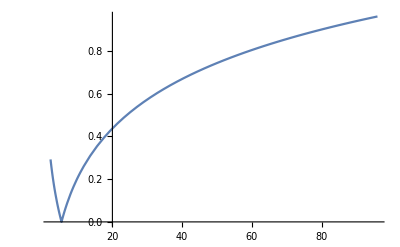

```mathematica
Plot[ratioCrossSection[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioCrossSection[(2mc)^2]
```

0.17076

```mathematica
CrossSectionRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

0.677236

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 mc)^2}],10^(-9)]
```

0.156147 z^3+0.914422 z^2

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 m)^2}],10^(-9)]
```

1.04296 z^3+0.914422 z^2